```mathematica
(* metric *)
(* coordinates r,theta grid*)

cx0=KSx0==x0;
cx3=KSx3==x3;
cx1=KSx1==R0+Exp[x1];
cx2=KSx2==(Tan[H0 Pi ((x2+(MY1+(2^MP0(MY2-MY1))/(R0+Exp[x1])^MP0)(1-2x2))-1/2)]/Tan[H0 Pi/2 ]+1)Pi/2;
suborg={cx0[[1]]->cx0[[2]],cx1[[1]]->cx1[[2]],cx2[[1]]->cx2[[2]],cx3[[1]]->cx3[[2]]}
R00=0;Rin=2.;Rout=10000; NX=64;H00=0.6;NY=64;miny=0.001;miny2=0.1;mpow=1.5;
grid=Table[{cx2[[2]]-π/2,cx1[[2]]}/.{R0->R00,H0->H00,MY1->miny,MY2->miny2,MP0->mpow},{x1,Log[Rin-R00],Log[Rout-R00],(Log[Rout-R00]-Log[Rin-R00])/NX},{x2,0,1,1/(NY+1)}];
```

{KSx0→x0,KSx1→ⅇ^x1+R0,KSx2→1/2 π (1+Cot[(H0 π)/2] Tan[H0 π (-1/2+(MY1+2^MP0 (-MY1+MY2) (ⅇ^x1+R0)^-MP0) (1-2 x2)+x2)]),KSx3→x3}

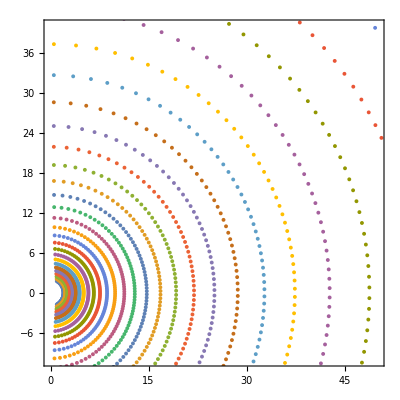

```mathematica
ListPolarPlot[grid,Frame->True,PlotRange->{{0,50},{-10,40}}]
```

```mathematica
cx2
cx2/.{x1->Log[KSx1-R0]}
```

KSx2==1/2 π (1+Cot[(H0 π)/2] Tan[H0 π (-1/2+(MY1+2^MP0 (-MY1+MY2) (ⅇ^x1+R0)^-MP0) (1-2 x2)+x2)])

KSx2==1/2 π (1+Cot[(H0 π)/2] Tan[H0 π (-1/2+(MY1+2^MP0 KSx1^-MP0 (-MY1+MY2)) (1-2 x2)+x2)])

```mathematica
Solve[KSx2== Tan[x2],x2]/.{C[1]->0}
```

{{x2→ArcTan[KSx2]}}

```mathematica
(* inverse transformation *)
subinv={
icx0=Solve[cx0,x0][[1,1]],
icx1=x1->Log[KSx1-R0],
icx2=Solve[cx2/.icx1,x2][[1,1]]/.{C[1]->0},
icx3=Solve[cx3,x3][[1,1]]}
```

{x0→KSx0,x1→Log[KSx1-R0],x2→(-H0 KSx1^MP0 π-2^(1+MP0) H0 MY1 π+2 H0 KSx1^MP0 MY1 π+2^(1+MP0) H0 MY2 π+2 KSx1^MP0 ArcTan[((-2 KSx2+π) Tan[(H0 π)/2])/π])/(2 H0 (-KSx1^MP0-2^(1+MP0) MY1+2 KSx1^MP0 MY1+2^(1+MP0) MY2) π),x3→KSx3}

```mathematica
dxdxMKSKS={{D[cx0[[2]],x0],D[cx0[[2]],x1],D[cx0[[2]],x2],D[cx0[[2]],x3]},
{D[cx1[[2]],x0],D[cx1[[2]],x1],D[cx1[[2]],x2],D[cx1[[2]],x3]},
{D[cx2[[2]],x0],D[cx2[[2]],x1],D[cx2[[2]],x2],D[cx2[[2]],x3]},
{D[cx3[[2]],x0],D[cx3[[2]],x1],D[cx3[[2]],x2],D[cx3[[2]],x3]}}//Simplify
```

{{1,0,0,0},{0,ⅇ^x1,0,0},{0,-2^(-1+MP0) ⅇ^x1 H0 MP0 (MY1-MY2) π^2 (ⅇ^x1+R0)^(-1-MP0) (-1+2 x2) Cot[(H0 π)/2] Sec[H0 π (-1/2+(MY1+2^MP0 (-MY1+MY2) (ⅇ^x1+R0)^-MP0) (1-2 x2)+x2)]^2,1/2 H0 π^2 (1-2 (MY1+2^MP0 (-MY1+MY2) (ⅇ^x1+R0)^-MP0)) Cot[(H0 π)/2] Sec[H0 π (-1/2+(MY1+2^MP0 (-MY1+MY2) (ⅇ^x1+R0)^-MP0) (1-2 x2)+x2)]^2,0},{0,0,0,1}}

```mathematica
TableForm[dxdxMKSKS]
```

1 | 0 | 0 | 0
0 | ⅇ^x1 | 0 | 0
0 | -2^(-1+MP0) ⅇ^x1 H0 MP0 (MY1-MY2) π^2 (ⅇ^x1+R0)^(-1-MP0) (-1+2 x2) Cot[(H0 π)/2] Sec[H0 π (-1/2+(MY1+2^MP0 (-MY1+MY2) (ⅇ^x1+R0)^-MP0) (1-2 x2)+x2)]^2 | 1/2 H0 π^2 (1-2 (MY1+2^MP0 (-MY1+MY2) (ⅇ^x1+R0)^-MP0)) Cot[(H0 π)/2] Sec[H0 π (-1/2+(MY1+2^MP0 (-MY1+MY2) (ⅇ^x1+R0)^-MP0) (1-2 x2)+x2)]^2 | 0
0 | 0 | 0 | 1

```mathematica
(* no coupling between various coordinates so this is simple *)
dxdxKSMKS=Inverse[dxdxMKSKS]/.subinv//Simplify;
TableForm[dxdxKSMKS]
```

1 | 0 | 0 | 0
0 | 1/(KSx1-R0) | 0 | 0
0 | -(2^(1+MP0) KSx1^(-1+MP0) MP0 (MY1-MY2) ArcTan[((-2 KSx2+π) Tan[(H0 π)/2])/π])/(H0 (KSx1^MP0 (1-2 MY1)+2^(1+MP0) (MY1-MY2))^2 π) | -(2 KSx1^MP0 Tan[(H0 π)/2])/(H0 (KSx1^MP0 (-1+2 MY1)+2^(1+MP0) (-MY1+MY2)) π^2 (1+((-2 KSx2+π)^2 Tan[(H0 π)/2]^2)/π^2)) | 0
0 | 0 | 0 | 1

```mathematica
TableForm[dxdxKSMKS/.{KSx1->3.1,R0->0,KSx2->Pi/4,H0->0.6,MY1->0.001,MY2->0.1}]
```

1 | 0 | 0 | 0
0 | 0.322581 | 0 | 0
0 | (0.0316574 2^(1+MP0) 3.1^(-1+MP0) MP0)/((-0.099 2^(1+MP0)+0.998 3.1^MP0)^2) | -(0.315454 3.1^MP0)/(0.099 2^(1+MP0)-0.998 3.1^MP0) | 0
0 | 0 | 0 | 1

```mathematica
(* done with dXdX arrays so far - no need for anything else - use METRICNUMERIC *)
```

```mathematica
(*************** CForms ******************)
```

```mathematica
substC={
"E"->"exp(1.0)"
};
```

```mathematica
(* coordinate transformations KS -> MKS *)
TableForm[{
CForm[subinv[[1,1]]],"="CForm[subinv[[1,2]]],";",
CForm[subinv[[2,1]]],"="CForm[subinv[[2,2]]],";",
CForm[subinv[[3,1]]],"="CForm[subinv[[3,2]]],";",
CForm[subinv[[4,1]]],"="CForm[subinv[[4,2]]],";"}]
```

x0
= KSx0
;
x1
= Log(KSx1 - R0)
;
x2
= (-(H0*Power(KSx1,MP0)*Pi) - Power(2,1 + MP0)*H0*MY1*Pi + 2*H0*Power(KSx1,MP0)*MY1*Pi + Power(2,1 + MP0)*H0*MY2*Pi + 2*Power(KSx1,MP0)*ArcTan(((-2*KSx2 + Pi)*Tan((H0*Pi)/2.))/Pi))/(2.*H0*(-Power(KSx1,MP0) - Power(2,1 + MP0)*MY1 + 2*Power(KSx1,MP0)*MY1 + Power(2,1 + MP0)*MY2)*Pi)
;
x3
= KSx3
;

```mathematica
(* coordinate transformations MKS -> KS *)
TableForm[{
CForm[suborg[[1,1]]],"="CForm[suborg[[1,2]]],";",
CForm[suborg[[2,1]]],"="CForm[suborg[[2,2]]],";",
CForm[suborg[[3,1]]],"="CForm[suborg[[3,2]]],";",
CForm[suborg[[4,1]]],"="CForm[suborg[[4,2]]],";"}]
```

KSx0
= x0
;
KSx1
= Power(E,x1) + R0
;
KSx2
= (Pi*(1 + Cot((H0*Pi)/2.)*Tan(H0*Pi*(-0.5 + (MY1 + (Power(2,MP0)*(-MY1 + MY2))/Power(Power(E,x1) + R0,MP0))*(1 - 2*x2) + x2))))/2.
;
KSx3
= x3
;

```mathematica
(* dxdx MKS -> KS in CForm *)
dxdxMKSKSc=TableForm[{
";dxdx[0][0]="CForm[dxdxMKSKS[[1,1]]],
";dxdx[0][1]="CForm[dxdxMKSKS[[1,2]]],
";dxdx[0][2]="CForm[dxdxMKSKS[[1,3]]],
";dxdx[0][3]="CForm[dxdxMKSKS[[1,4]]],
";dxdx[1][0]="CForm[dxdxMKSKS[[2,1]]],
";dxdx[1][1]="CForm[dxdxMKSKS[[2,2]]],
";dxdx[1][2]="CForm[dxdxMKSKS[[2,3]]],
";dxdx[1][3]="CForm[dxdxMKSKS[[2,4]]],
";dxdx[2][0]="CForm[dxdxMKSKS[[3,1]]],
";dxdx[2][1]="CForm[dxdxMKSKS[[3,2]]],
";dxdx[2][2]="CForm[dxdxMKSKS[[3,3]]],
";dxdx[2][3]="CForm[dxdxMKSKS[[3,4]]],
";dxdx[3][0]="CForm[dxdxMKSKS[[4,1]]],
";dxdx[3][1]="CForm[dxdxMKSKS[[4,2]]],
";dxdx[3][2]="CForm[dxdxMKSKS[[4,3]]],
";dxdx[3][3]="CForm[dxdxMKSKS[[4,4]]],";"
}]
```

;dxdx[0][0]= 1
;dxdx[0][1]= 0
;dxdx[0][2]= 0
;dxdx[0][3]= 0
;dxdx[1][0]= 0
;dxdx[1][1]= Power(E,x1)
;dxdx[1][2]= 0
;dxdx[1][3]= 0
;dxdx[2][0]= 0
;dxdx[2][1]= -(Power(2,-1 + MP0)*Power(E,x1)*H0*MP0*(MY1 - MY2)*Power(Pi,2)*Power(Power(E,x1) + R0,-1 - MP0)*(-1 + 2*x2)*Cot((H0*Pi)/2.)*Power(Sec(H0*Pi*(-0.5 + (MY1 + (Power(2,MP0)*(-MY1 + MY2))/Power(Power(E,x1) + R0,MP0))*(1 - 2*x2) + x2)),2))
;dxdx[2][2]= (H0*Power(Pi,2)*(1 - 2*(MY1 + (Power(2,MP0)*(-MY1 + MY2))/Power(Power(E,x1) + R0,MP0)))*Cot((H0*Pi)/2.)*Power(Sec(H0*Pi*(-0.5 + (MY1 + (Power(2,MP0)*(-MY1 + MY2))/Power(Power(E,x1) + R0,MP0))*(1 - 2*x2) + x2)),2))/2.
;dxdx[2][3]= 0
;dxdx[3][0]= 0
;dxdx[3][1]= 0
;dxdx[3][2]= 0
;dxdx[3][3]= 1
;

```mathematica
(* dxdx KS -> MKS in CForm *)
dxdxKSMKSc=TableForm[{
";dxdx[0][0]="CForm[dxdxKSMKS[[1,1]]],
";dxdx[0][1]="CForm[dxdxKSMKS[[1,2]]],
";dxdx[0][2]="CForm[dxdxKSMKS[[1,3]]],
";dxdx[0][3]="CForm[dxdxKSMKS[[1,4]]],
";dxdx[1][0]="CForm[dxdxKSMKS[[2,1]]],
";dxdx[1][1]="CForm[dxdxKSMKS[[2,2]]],
";dxdx[1][2]="CForm[dxdxKSMKS[[2,3]]],
";dxdx[1][3]="CForm[dxdxKSMKS[[2,4]]],
";dxdx[2][0]="CForm[dxdxKSMKS[[3,1]]],
";dxdx[2][1]="CForm[dxdxKSMKS[[3,2]]],
";dxdx[2][2]="CForm[dxdxKSMKS[[3,3]]],
";dxdx[2][3]="CForm[dxdxKSMKS[[3,4]]],
";dxdx[3][0]="CForm[dxdxKSMKS[[4,1]]],
";dxdx[3][1]="CForm[dxdxKSMKS[[4,2]]],
";dxdx[3][2]="CForm[dxdxKSMKS[[4,3]]],
";dxdx[3][3]="CForm[dxdxKSMKS[[4,4]]],";"
}]
```

;dxdx[0][0]= 1
;dxdx[0][1]= 0
;dxdx[0][2]= 0
;dxdx[0][3]= 0
;dxdx[1][0]= 0
;dxdx[1][1]= 1/(KSx1 - R0)
;dxdx[1][2]= 0
;dxdx[1][3]= 0
;dxdx[2][0]= 0
;dxdx[2][1]= -((Power(2,1 + MP0)*Power(KSx1,-1 + MP0)*MP0*(MY1 - MY2)*ArcTan(((-2*KSx2 + Pi)*Tan((H0*Pi)/2.))/Pi))/(H0*Power(Power(KSx1,MP0)*(1 - 2*MY1) + Power(2,1 + MP0)*(MY1 - MY2),2)*Pi))
;dxdx[2][2]= (-2*Power(KSx1,MP0)*Tan((H0*Pi)/2.))/(H0*(Power(KSx1,MP0)*(-1 + 2*MY1) + Power(2,1 + MP0)*(-MY1 + MY2))*Power(Pi,2)*(1 + (Power(-2*KSx2 + Pi,2)*Power(Tan((H0*Pi)/2.),2))/Power(Pi,2)))
;dxdx[2][3]= 0
;dxdx[3][0]= 0
;dxdx[3][1]= 0
;dxdx[3][2]= 0
;dxdx[3][3]= 1
;